```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/humayrajeba/Documents/Wolfram Mathematica/processed_data_dBm"];
data=Import["updated_video_2.txt","Table"];
micromobility=data⟦All,2⟧;
SetDirectory["/Users/humayrajeba/Documents/Wolfram Mathematica/THzBlock"];
data=Import["Set3_H=135cm_L13=450cm_L12=300cm/DATA_UNCAL_Meas22","Table"];
avgParam=20;
percentage=5;
blockage=data⟦All,2⟧;
```

```mathematica
micromobility
blockage
```

```mathematica
(*Calculate the weighted signal and its exponential moving average*)
block1=10*Log10[blockage]
```

```mathematica
micro1=Take[micromobility]
```

-Graphics-

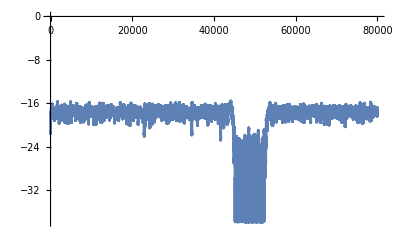

```mathematica
microPeriodogram=PeriodogramArray@micro1
ListLinePlot[micro1,PlotRange->All]

blockPeriodogram=PeriodogramArray@block1
ListLinePlot[block1+35,PlotRange->All]
```

```mathematica
microPeriodogram=PeriodogramArray[micro1];
blockPeriodogram=PeriodogramArray[block1];

ListLinePlot[{micro1,block1+35},PlotRange->All,PlotLegends->{"Micro1","Block1"}]
```

-Graphics-

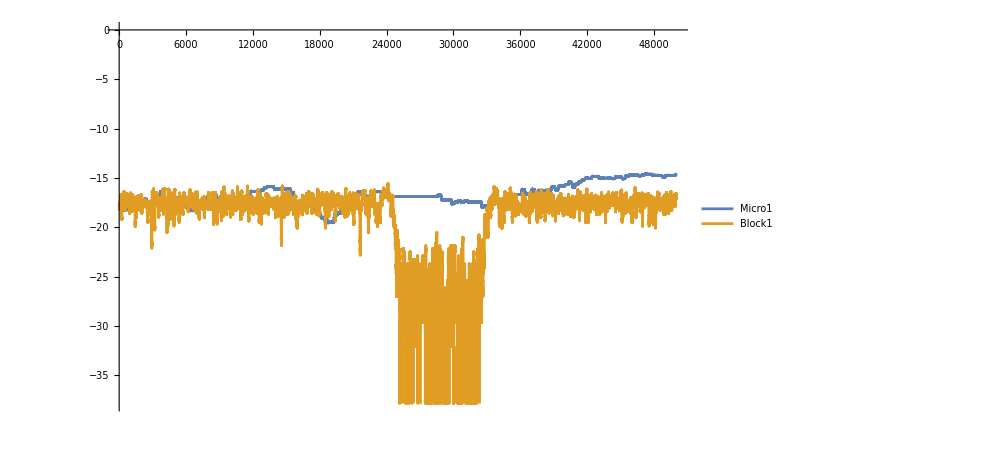

```mathematica
ListLinePlot[{micro1[[30000;;80000]],block1[[20000;;70000]]+35},PlotRange->All,PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro1","Block1"},{0.6,0.8}]]
```

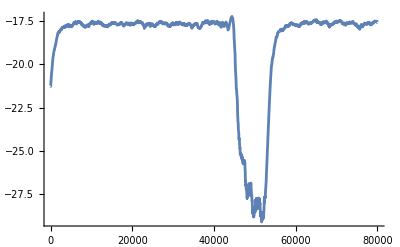

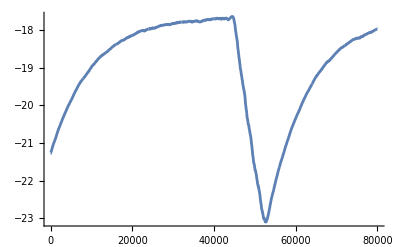

```mathematica
block=block1+35
decayRate1=0.001;
movingAvg1=Re[ExponentialMovingAverage[block,decayRate1]]
ListLinePlot[movingAvg1,PlotRange->All]
decayRate2=0.0001;
movingAvg2=Re[ExponentialMovingAverage[block,decayRate2]]
ListLinePlot[movingAvg2,PlotRange->All]
```

```mathematica
movingAvg3=Re[ExponentialMovingAverage[micromobility,decayRate1]]
ListLinePlot[movingAvg3,PlotRange->All]
movingAvg4=Re[ExponentialMovingAverage[micromobility,decayRate2]]
ListLinePlot[movingAvg4,PlotRange->All]
```

-Graphics-

-Graphics-

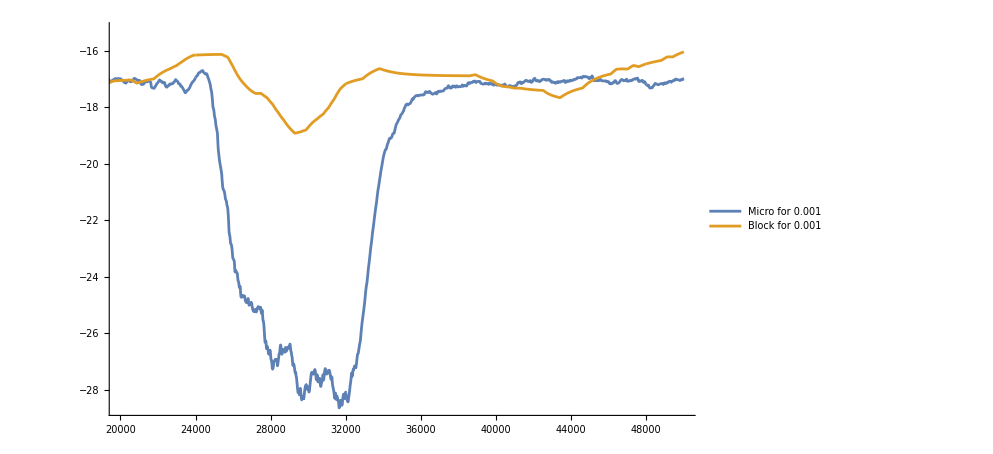

```mathematica
ListLinePlot[{movingAvg1[[20000;;70000]]+0.5,movingAvg3[[20000;;70000]]},PlotRange->{{20000,50000},All},PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro for 0.001","Block for 0.001"},{0.8,0.5}]]
```

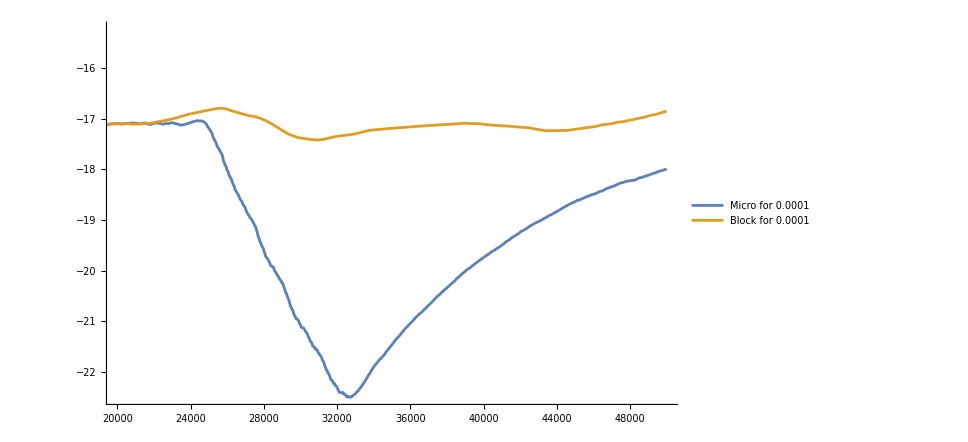

```mathematica
ListLinePlot[{movingAvg2[[20000;;70000]]+0.6,movingAvg4[[20000;;70000]]},PlotRange->{{20000,50000},All},PlotStyle->{BlueGray},PlotLegends->Placed[{"Micro for 0.0001","Block for 0.0001"},{0.5,0.5}]]
```

```mathematica
(*Initialize the list to store the sum of periodograms without decay rate*)
sumPeriodograms={};

(*Calculate the number of segments*)
numSegments=Quotient[Length[block],500];

(*Loop through each segment*)
For[i=1,i<=numSegments,i++,
(*Extract the i^th segment of 500 values*)
blockSegment=Take[block,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram=PeriodogramArray[blockSegment];
(*Sum up the values of the periodogram*)
sumPeriodogram=Total[periodogram];
(*Append the sum to the list*)
AppendTo[sumPeriodograms,sumPeriodogram];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms
```

{156999.,159843.,155849.,153551.,158178.,156125.,156326.,159035.,157153.,157208.,156418.,149249.,155707.,152467.,156637.,161624.,159546.,156356.,155529.,151034.,153419.,156424.,154742.,155509.,155609.,160251.,159306.,159335.,153034.,153201.,153846.,155668.,158504.,155335.,153345.,161077.,152272.,155984.,159612.,153391.,155270.,152797.,152931.,152132.,157041.,167167.,151092.,156117.,157649.,158272.,158941.,153130.,152008.,153188.,157202.,156422.,157334.,159512.,155373.,153678.,156579.,153470.,156628.,153892.,157786.,159170.,155919.,152878.,161399.,157743.,152836.,161951.,162691.,153864.,149983.,153853.,151807.,159749.,153673.,149952.,157470.,154153.,156199.,159331.,161516.,148977.,172525.,139896.,145235.,218742.,338821.,383502.,382763.,349751.,357320.,456513.,371662.,369374.,507946.,421076.,389181.,407920.,462813.,421187.,373314.,247803.,166089.,140815.,165437.,155582.,154501.,157315.,158951.,161149.,153546.,158947.,153414.,153265.,158005.,157873.,157948.,159537.,150529.,151908.,154146.,157435.,154610.,153991.,149352.,152559.,157103.,156552.,157422.,152207.,150130.,163362.,156734.,155817.,151588.,151227.,154670.,151846.,159991.,153676.,156325.,154975.,153288.,152011.,160342.,159806.,161912.,154936.,158756.,153378.,154618.,153180.,159240.,152576.,150147.,154137.}

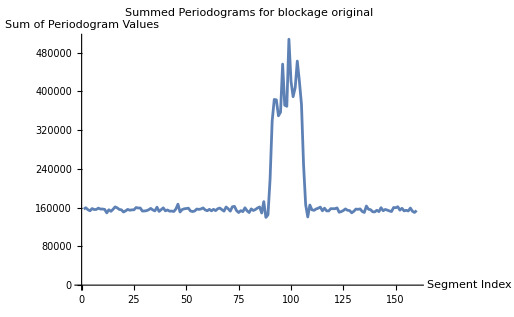

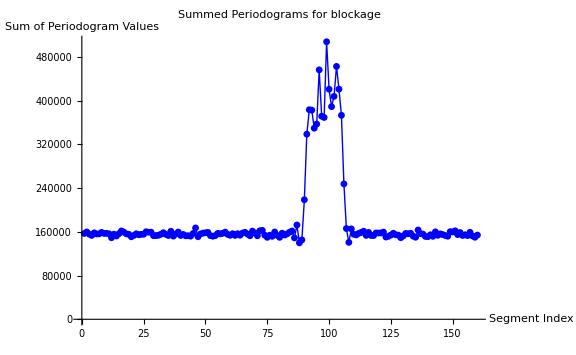

```mathematica
(*Plot the summed periodograms for blockage trace*)
ListLinePlot[sumPeriodograms,PlotRange->All,
PlotLabel->"Summed Periodograms for blockage original",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for blockage",AxesLabel->{"Segment Index","Sum of Periodogram Values"},ImageSize->Large]
```

```mathematica
(*Initialize the list to store the sum of periodograms without decay rate*)
sumPeriodograms1={};

(*Calculate the number of segments*)
numSegments1=Quotient[Length[micromobility],500];

(*Loop through each segment*)
For[i=1,i<=numSegments1,i++,
(*Extract the i^th segment of 500 values*)
microSegment1=Take[micromobility,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram1=PeriodogramArray[microSegment1];
(*Sum up the values of the periodogram*)
sumPeriodogram1=Total[periodogram1];
(*Append the sum to the list*)
AppendTo[sumPeriodograms1,sumPeriodogram1];]

(*Output the list of summed periodograms for micromobility*)
sumPeriodograms1
```

{110849.,112203.,110571.,110388.,110277.,109584.,108979.,112722.,116241.,113930.,113596.,112978.,112301.,112785.,115181.,116934.,116861.,118988.,119481.,122672.,122283.,120766.,119840.,119745.,118385.,118165.,118759.,119194.,119347.,119512.,118080.,118826.,117612.,116517.,115418.,116588.,116394.,116404.,117423.,117888.,116094.,117389.,119496.,124814.,127945.,133153.,137300.,142911.,147165.,147465.,145418.,143993.,146799.,147694.,173063.,179712.,186323.,182380.,179554.,163277.,162983.,164354.,161888.,150217.,147698.,152831.,145669.,136757.,148194.,146794.,145340.,154859.,163568.,164944.,162416.,150355.,140209.,144807.,144099.,144174.,144939.,149094.,142691.,138929.,134178.,132660.,127203.,127123.,130056.,130020.,131337.,146961.,161198.,160891.,156246.,166783.,180277.,188169.,184051.,170648.,160690.,155071.,141509.,137160.,142339.,140714.,134368.,137746.,142680.,142730.,142592.,142701.,142663.,142739.,142744.,142699.,142782.,142232.,148322.,150781.,152406.,151553.,151043.,152165.,152227.,159708.,156763.,147558.,147555.,140640.,139318.,139340.,134019.,138524.,134119.,133860.,132279.,129609.,129196.,125237.,121731.,123909.,120266.,114592.,112705.,110270.,112571.,112695.,113377.,111073.,112503.,109276.,108143.,108867.,107208.,107663.,108737.,110141.,108875.,108518.,107178.,106847.,107315.,107386.,107382.,107365.,107355.,108401.,108764.,108504.,108775.,108152.,108027.,108261.,108735.,109057.,111008.,111066.,111047.,109769.,108718.,112483.,115081.,112873.,113585.,114218.,115074.,116595.,115290.,117082.,117923.,121747.,125252.,125302.,125195.,126753.,127312.,123249.,120978.,118569.,119115.,120105.,118291.,116009.,116617.,114361.,111758.,111486.,111549.,110358.,109801.,109856.,109850.,111482.,111067.,107802.,107568.,107561.,107552.,106979.,107298.,107447.,107431.,107096.,107223.,106656.,106709.,108002.,110115.,110065.,109696.,109579.,108367.,106922.,106887.,106899.,106839.,108659.,108742.,108793.,110605.,111854.,112385.,111288.,110361.,110041.,109984.,109987.,108220.,107951.,108120.,109183.,109976.,110040.,110723.,113222.,113025.,112066.,112049.,111753.,112056.,111895.,110235.,108996.,112030.,112957.,110706.,108754.,108312.,108692.,108175.,109062.,110566.,109707.,109790.,109388.,107625.,108418.,109046.,108945.,112062.,114607.,112915.,113303.,114372.,117996.,119253.,119396.,118885.,117322.,114875.,112267.,111949.,116687.,118020.,119271.,119712.,114601.,117605.,119535.,116904.,116646.,115637.,111338.,109613.,110262.,110014.,113560.,113360.,113265.,112024.,111606.,111416.,112985.,112996.,112952.,110358.,109566.,113281.,117164.,116993.,114491.,113054.,115346.,113931.,115750.,114230.,113073.,113043.,114782.,115884.,115887.,113985.,114430.,114490.,113741.,111959.,111471.,110871.,110855.,111812.,108366.,108393.,109283.,109309.,109303.,109323.,109678.,111556.,108424.,108000.,108825.,108555.,108108.,108254.,108402.,108540.,109255.,109287.,108975.,110410.,112450.,112699.,112118.,112888.,113800.,114193.,116743.,119353.,121084.,117268.,117099.,117077.,117796.,120891.,118119.,116543.,115839.,115704.,115817.,115724.,115825.,116519.,116470.,115683.,112160.,112333.,115503.,115532.,115483.,114049.,110753.,110670.,111300.,114347.,114635.,115973.,114510.,113733.,113516.,112028.,113482.,112412.,112644.,112307.,113407.,116728.,119269.,115556.,111489.,111702.,111641.,108889.,108833.,108097.,107366.,107010.,108033.,109142.,111808.,111631.,109594.,111629.,113647.,115042.,117139.,118313.,115698.,115892.,116598.,118628.,117215.,115176.,114668.,115615.,115812.,115303.,113221.,114501.,115642.,114994.,113494.,114092.,115510.,116632.,116834.,116785.,116214.,120642.,119567.,120926.,121017.,119717.,118465.,115298.,113034.,112324.,111345.,112155.,111430.,109334.,108729.,110725.,114565.,115272.,113429.,113884.,114013.,115550.,109593.,110103.,110053.,109877.,109373.,107919.,107972.,108794.,108799.,108628.,108088.,108198.,109523.,108833.,110140.,110384.,109839.,109787.,109792.,110846.,110847.,110079.,110841.,111814.,112986.,113034.,114145.,116287.,115245.,110984.,109881.,109656.,109679.,110849.,111778.,113191.,113095.,113818.,113751.,118891.,124144.,125347.,124351.,127704.,130434.,125212.,123129.,121373.,120347.,123802.,125983.,130860.,134620.,131826.,129155.,126049.,123634.,121512.,121526.,119255.,119159.,117910.,117225.,119615.,120152.,121290.,120968.,120522.,118058.,123733.,125909.,122933.,122950.,129391.,126986.,128494.,128880.,130468.,127151.,126744.,122824.,121517.,128638.,129097.,130353.,127986.,127140.,127140.,128173.,126031.,123985.,127566.,131824.,129595.,127289.,124847.,131282.,137859.,136846.,138091.,138012.,132055.,129396.,127355.,131959.,133778.,134267.,127782.,126281.,123421.,124201.,117342.,110829.,111762.,111149.,109924.,109110.,110644.,111186.,111253.,111321.,112545.,114388.,116523.,117354.,118285.,120422.,120047.,119810.,119195.,119424.}

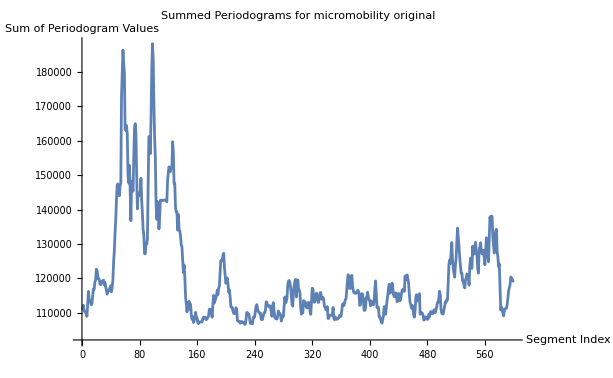

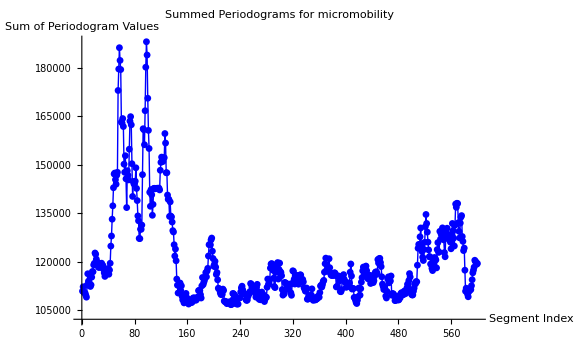

```mathematica
(*Plot the summed periodograms*)
ListLinePlot[sumPeriodograms1,PlotRange->All,
PlotLabel->"Summed Periodograms for micromobility original",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms1,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for micromobility",AxesLabel->{"Segment Index","Sum of Periodogram Values"},ImageSize->Large]
```

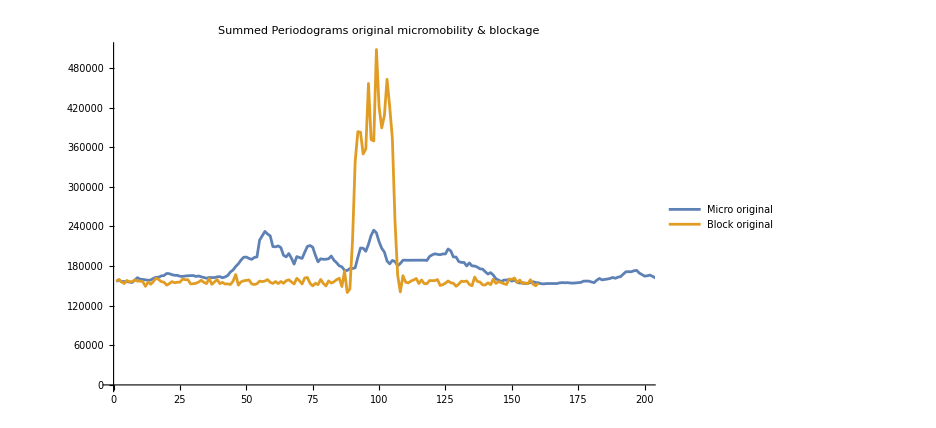

```mathematica
ListLinePlot[{sumPeriodograms1+46150,sumPeriodograms},PlotRange->{{0,200},All},PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms original micromobility & blockage",PlotLegends->Placed[{"Micro original","Block original"},{0.2,0.8}]]
```

{211545.,188097.,177028.,166887.,163123.,160396.,158995.,158134.,157115.,157829.,157540.,154939.,154395.,153467.,154138.,156403.,158057.,157778.,157350.,155078.,153549.,155176.,154684.,154122.,154827.,156413.,157523.,157972.,156831.,155834.,154735.,154643.,155983.,156001.,154740.,156609.,156031.,155343.,155719.,155671.,156020.,154754.,153155.,153714.,154276.,157113.,157423.,156042.,156178.,156287.,157392.,156923.,155327.,153772.,154483.,155178.,155049.,157141.,157238.,155249.,155761.,155001.,155348.,154839.,155955.,156027.,156913.,155423.,156733.,158259.,156127.,155680.,159391.,158880.,155068.,153817.,153450.,154751.,154503.,153508.,154550.,153953.,155476.,157063.,155718.,155836.,158189.,157008.,149628.,158454.,203362.,255011.,302677.,321472.,329173.,356038.,377692.,366629.,384980.,408684.,393803.,394350.,399039.,416630.,400388.,357087.,286973.,227564.,196057.,181796.,170401.,164381.,162165.,162037.,159703.,158142.,157530.,155280.,155724.,156423.,156984.,157846.,155972.,154550.,154018.,153983.,155241.,154590.,153196.,152137.,153375.,154408.,155547.,154277.,153844.,154651.,157715.,156345.,155033.,153664.,153298.,152931.,153858.,155198.,155762.,155011.,154455.,153867.,155059.,156405.,158784.,159289.,157373.,155831.,155496.,154552.,155409.,155037.,153526.,153331.}

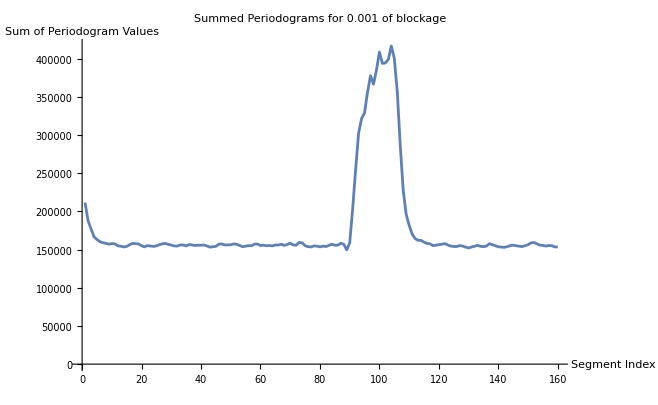

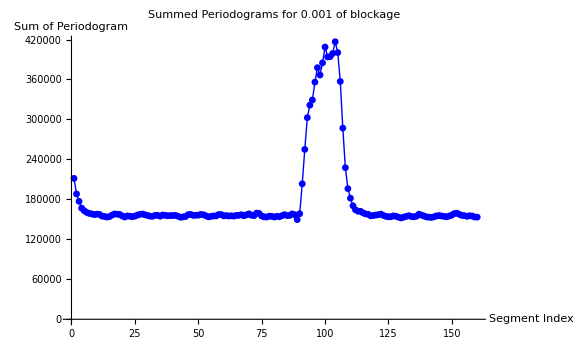

```mathematica
(*Initialize the list to store the sum of periodograms with 0.001 decay rate for blockage*)
sumPeriodograms2={};

(*Calculate the number of segments*)
numSegments2=Quotient[Length[movingAvg1],500];

(*Loop through each segment*)
For[i=1,i<=numSegments2,i++,
(*Extract the i^th segment of 500 values*)
blockSegment2=Take[movingAvg1,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram2=PeriodogramArray[blockSegment2];
(*Sum up the values of the periodogram*)
sumPeriodogram2=Total[periodogram2];
(*Append the sum to the list*)
AppendTo[sumPeriodograms2,sumPeriodogram2];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms2
(*Plot the summed periodograms for 0.001*)
ListLinePlot[sumPeriodograms2,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.001 of blockage",
AxesLabel->{"Segment Index","Sum of Periodogram Values"}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms2,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.001 of blockage",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

{110050.,110828.,110961.,110769.,110595.,110379.,109880.,110031.,112103.,113225.,113524.,113260.,113168.,112767.,113195.,114448.,115496.,116349.,117438.,119072.,120315.,120935.,120549.,120416.,119726.,119131.,118990.,118958.,118977.,119095.,119176.,118671.,118650.,117989.,117123.,116706.,116618.,116521.,116614.,117154.,117062.,116875.,117310.,119481.,122193.,125433.,129363.,133538.,138267.,141833.,143812.,143674.,144773.,144878.,151633.,161359.,170049.,175407.,178087.,175090.,169641.,167753.,166110.,161767.,156268.,154202.,152332.,147558.,145539.,146249.,146200.,147465.,152246.,157405.,160026.,158495.,152490.,148084.,147338.,145778.,145395.,146245.,145831.,144198.,140654.,137880.,134600.,131421.,130481.,130300.,130278.,133211.,142415.,149551.,153216.,155948.,163023.,171492.,177995.,177298.,171951.,166662.,159140.,150402.,146424.,144751.,141498.,138997.,139941.,141034.,141667.,142052.,142298.,142458.,142574.,142631.,142672.,142420.,143813.,145793.,148531.,149652.,150268.,150907.,151415.,153328.,155522.,153678.,151258.,148549.,144860.,142674.,140261.,138660.,137314.,136585.,134946.,133573.,131650.,129827.,127429.,125243.,124312.,121446.,118244.,115437.,113864.,113402.,113227.,112851.,112451.,111847.,110492.,109741.,109070.,108320.,108357.,108711.,109124.,108968.}

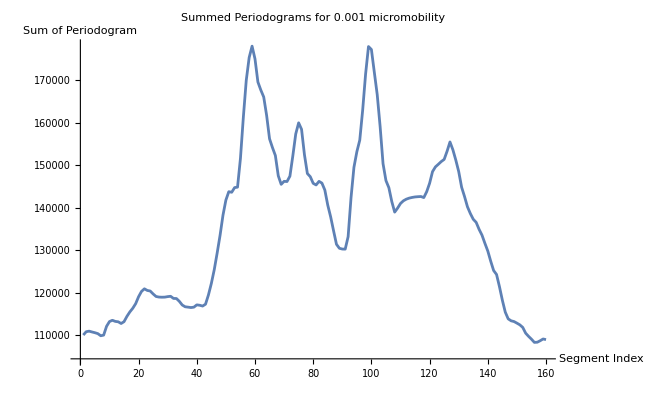

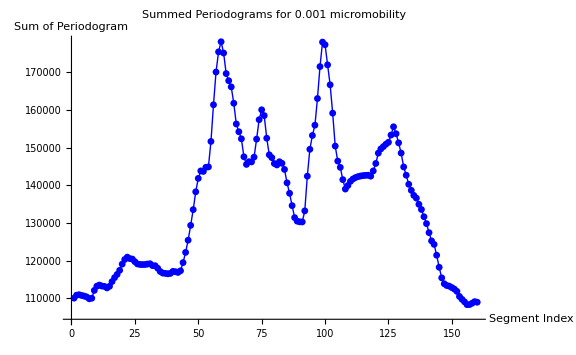

```mathematica
(*Initialize the list to store the sum of periodograms with 0.001 decay rate for micromobility*)
sumPeriodograms3={};

(*Calculate the number of segments*)
numSegments3=Quotient[Length[movingAvg3],500];

(*Loop through each segment*)
For[i=1,i<=numSegments2,i++,
(*Extract the i^th segment of 500 values*)
blockSegment3=Take[movingAvg3,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram3=PeriodogramArray[blockSegment3];
(*Sum up the values of the periodogram*)
sumPeriodogram3=Total[periodogram3];
(*Append the sum to the list*)
AppendTo[sumPeriodograms3,sumPeriodogram3];]

(*Output the list of summed periodograms for micromobility trace*)
sumPeriodograms3
(*Plot the summed periodograms for 0.001*)
ListLinePlot[sumPeriodograms3,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.001 micromobility",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms3,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.001 micromobility",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

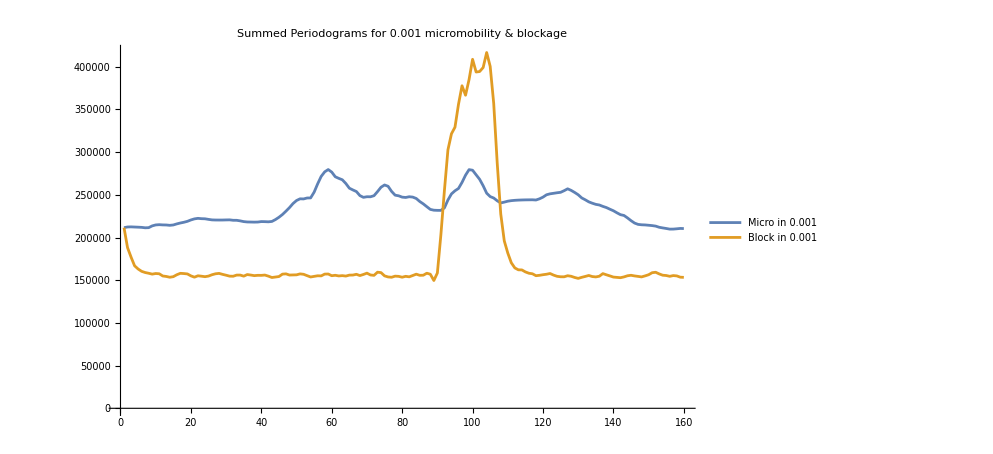

```mathematica
ListLinePlot[{sumPeriodograms3+101495,sumPeriodograms2},PlotRange->All,PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms for 0.001 micromobility & blockage",PlotLegends->Placed[{"Micro in 0.001","Block in 0.001"},{0.2,0.8}]]
```

{224595.,220873.,217723.,214243.,211257.,208389.,205702.,203166.,200697.,198544.,196413.,194067.,191968.,189922.,188138.,186701.,185382.,183975.,182586.,181021.,179499.,178407.,177166.,175956.,174949.,174140.,173402.,172669.,171802.,170928.,170027.,169252.,168691.,168070.,167310.,166910.,166345.,165737.,165268.,164797.,164387.,163819.,163166.,162743.,162361.,162301.,162110.,161703.,161429.,161191.,161084.,160859.,160464.,160015.,159785.,159615.,159384.,159425.,159333.,158989.,158867.,158623.,158479.,158263.,158232.,158126.,158142.,157901.,157926.,158070.,157819.,157669.,158026.,158046.,157616.,157335.,157122.,157085.,156953.,156710.,156674.,156501.,156566.,156697.,156539.,156544.,156752.,156740.,155821.,156480.,161610.,168925.,177424.,184603.,191149.,199380.,208111.,214173.,222238.,231512.,237604.,244363.,251169.,259417.,264720.,266293.,262631.,256436.,250670.,245861.,240849.,236242.,232111.,228385.,224560.,220903.,217513.,214041.,211008.,208220.,205604.,203199.,200606.,198093.,195769.,193607.,191750.,189791.,187810.,185886.,184319.,182886.,181600.,180118.,178756.,177586.,176841.,175706.,174570.,173407.,172368.,171366.,170546.,169897.,169241.,168470.,167731.,167002.,166485.,166098.,165908.,165640.,165071.,164511.,164031.,163494.,163155.,162735.,162168.,161706.}

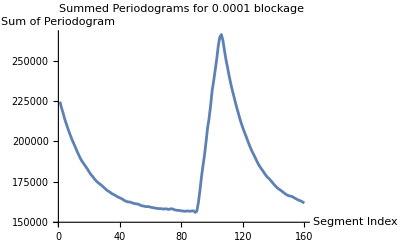

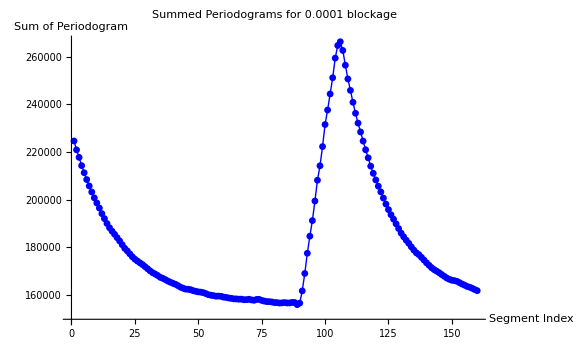

```mathematica
(*Initialize the list to store the sum of periodograms with 0.0001 decay rate for blockage*)
sumPeriodograms4={};

(*Calculate the number of segments*)
numSegments4=Quotient[Length[movingAvg2],500];

(*Loop through each segment*)
For[i=1,i<=numSegments4,i++,
(*Extract the i^th segment of 500 values*)
blockSegment4=Take[movingAvg2,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram4=PeriodogramArray[blockSegment4];
(*Sum up the values of the periodogram*)
sumPeriodogram4=Total[periodogram4];
(*Append the sum to the list*)
AppendTo[sumPeriodograms4,sumPeriodogram4];]

(*Output the list of summed periodograms for blockage trace*)
sumPeriodograms4
(*Plot the summed periodograms for 0.0001*)
ListLinePlot[sumPeriodograms4,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.0001 blockage",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms4,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.0001 blockage",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

{109988.,110084.,110140.,110157.,110165.,110161.,110111.,110111.,110357.,110584.,110749.,110852.,110959.,111016.,111149.,111400.,111676.,111960.,112304.,112743.,113198.,113617.,113924.,114227.,114444.,114627.,114827.,115023.,115215.,115412.,115603.,115712.,115856.,115912.,115909.,115914.,115942.,115963.,116000.,116095.,116139.,116158.,116244.,116552.,117019.,117650.,118486.,119489.,120700.,121941.,123108.,124067.,125111.,126050.,127669.,129876.,132282.,134607.,136768.,138352.,139437.,140626.,141710.,142374.,142649.,143043.,143366.,143236.,143173.,143380.,143517.,143784.,144529.,145518.,146402.,146892.,146742.,146472.,146461.,146309.,146234.,146288.,146249.,146033.,145507.,144921.,144165.,143283.,142565.,141940.,141356.,141150.,141887.,142787.,143565.,144336.,145704.,147498.,149377.,150657.,151306.,151671.,151511.,150815.,150289.,149891.,149240.,148532.,148171.,147903.,147644.,147398.,147166.,146947.,146741.,146544.,146357.,146147.,146125.,146255.,146567.,146802.,147017.,147251.,147490.,147900.,148433.,148569.,148520.,148333.,147885.,147462.,146935.,146391.,145847.,145333.,144692.,144037.,143269.,142464.,141529.,140532.,139654.,138518.,137238.,135909.,134655.,133539.,132494.,131473.,130475.,129492.,128423.,127415.,126437.,125459.,124597.,123822.,123120.,122397.,121663.,120920.,120230.,119585.,118975.,118395.,117845.,117343.,116915.,116502.,116102.,115743.,115356.,114992.,114676.,114390.,114174.,114023.,113877.,113713.,113485.,113338.,113385.,113391.,113381.,113409.,113464.,113604.,113701.,113809.,114001.,114253.,114725.,115229.,115709.,116190.,116716.,117154.,117367.,117476.,117540.,117647.,117743.,117704.,117615.,117536.,117302.,117017.,116746.,116465.,116144.,115832.,115537.,115285.,115106.,114825.,114465.,114123.,113799.,113479.,113154.,112877.,112608.,112348.,112086.,111838.,111580.,111358.,111261.,111202.,111144.,111061.,110972.,110798.,110606.,110423.,110247.,110111.,110063.,109986.,109977.,110028.,110144.,110234.,110258.,110250.,110239.,110227.,110177.,110068.,109966.,109900.,109889.,109895.,109914.,110005.,110174.,110296.,110355.,110445.,110512.,110595.,110610.,110559.,110540.,110667.,110715.,110672.,110556.,110458.,110356.,110258.,110246.,110255.,110219.,110196.,110110.,109989.,109945.,109895.,109914.,110093.,110268.,110401.,110561.,110831.,111215.,111611.,111968.,112286.,112452.,112518.,112458.,112559.,112797.,113072.,113411.,113588.,113674.,113946.,114133.,114260.,114371.,114328.,114108.,113919.,113729.,113629.,113630.,113612.,113581.,113477.,113369.,113324.,113308.,113292.,113225.,113037.,112959.,113080.,113279.,113416.,113410.,113445.,113507.,113570.,113652.,113640.,113612.,113615.,113710.,113833.,113868.,113881.,113918.,113931.,113870.,113770.,113636.,113500.,113394.,113250.,112990.,112786.,112615.,112452.,112298.,112154.,112086.,111998.,111787.,111630.,111490.,111331.,111174.,111036.,110907.,110812.,110736.,110658.,110602.,110648.,110748.,110826.,110908.,111020.,111171.,111374.,111683.,112109.,112453.,112676.,112890.,113097.,113405.,113717.,113877.,113994.,114075.,114158.,114237.,114311.,114402.,114503.,114589.,114563.,114411.,114409.,114463.,114513.,114542.,114422.,114234.,114077.,114002.,114041.,114106.,114163.,114157.,114120.,114059.,113993.,113952.,113881.,113803.,113772.,113799.,114034.,114209.,114171.,114015.,113931.,113731.,113497.,113250.,112977.,112682.,112426.,112236.,112146.,112136.,112063.,111981.,112024.,112122.,112325.,112575.,112817.,112934.,113106.,113328.,113548.,113668.,113733.,113799.,113897.,113988.,113989.,113982.,114034.,114106.,114098.,114090.,114114.,114215.,114347.,114460.,114548.,114735.,115025.,115244.,115546.,115768.,115946.,115983.,115895.,115725.,115536.,115338.,115192.,114940.,114642.,114397.,114298.,114349.,114340.,114313.,114293.,114339.,114237.,114013.,113819.,113636.,113435.,113205.,112931.,112713.,112521.,112337.,112138.,111941.,111788.,111660.,111550.,111496.,111425.,111346.,111270.,111214.,111214.,111167.,111129.,111133.,111206.,111292.,111405.,111588.,111795.,111856.,111788.,111685.,111586.,111514.,111512.,111552.,111636.,111727.,111825.,112006.,112485.,113094.,113638.,114207.,114948.,115560.,115969.,116270.,116480.,116715.,117123.,117658.,118400.,119099.,119670.,120007.,120273.,120364.,120421.,120421.,120359.,120281.,120116.,120053.,120040.,120067.,120130.,120174.,120110.,120120.,120391.,120563.,120684.,120927.,121307.,121607.,121954.,122340.,122644.,122845.,122963.,122878.,122971.,123289.,123598.,123879.,124046.,124195.,124353.,124507.,124519.,124555.,124829.,125130.,125273.,125316.,125392.,125847.,126449.,126935.,127526.,127851.,128005.,127999.,128051.,128330.,128582.,128741.,128622.,128438.,128197.,127919.,127141.,126346.,125598.,124843.,124061.,123347.,122733.,122159.,121614.,121135.,120752.,120482.,120322.,120183.,120159.,120166.,120151.,120125.,120064.}

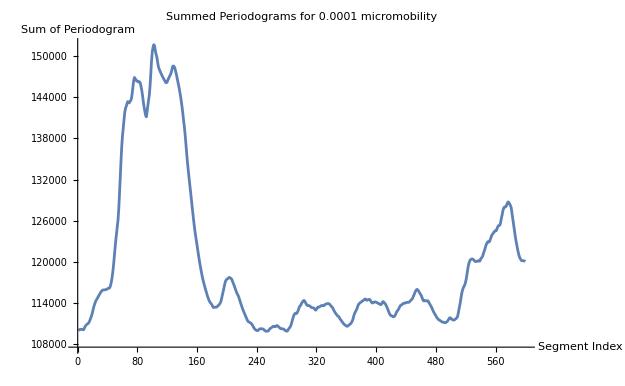

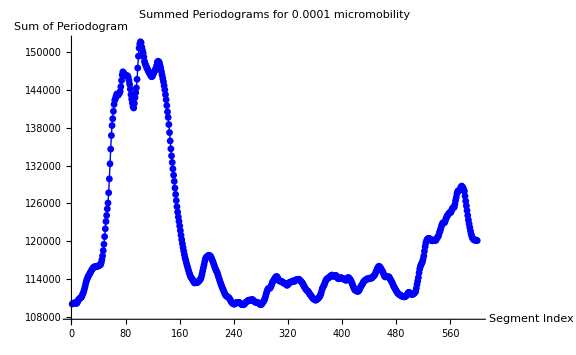

```mathematica
(*Initialize the list to store the sum of periodograms with 0.0001 decay rate for micromobility*)
sumPeriodograms5={};

(*Calculate the number of segments*)
numSegments5=Quotient[Length[movingAvg4],500];

(*Loop through each segment*)
For[i=1,i<=numSegments5,i++,
(*Extract the i^th segment of 500 values*)
blockSegment5=Take[movingAvg4,{500*(i-1)+1,500*i}];
(*Compute the periodogram for the current segment*)
periodogram5=PeriodogramArray[blockSegment5];
(*Sum up the values of the periodogram*)
sumPeriodogram5=Total[periodogram5];
(*Append the sum to the list*)
AppendTo[sumPeriodograms5,sumPeriodogram5];]

(*Output the list of summed periodograms for micromobility trace*)
sumPeriodograms5
(*Plot the summed periodograms for 0.0001*)
ListLinePlot[sumPeriodograms5,PlotRange->All,
PlotLabel->"Summed Periodograms for 0.0001 micromobility",
AxesLabel->{"Segment Index","Sum of Periodogram "}]
(*Plot the summed periodograms with smaller dots and thinner lines*)ListPlot[sumPeriodograms5,Joined->True,PlotStyle->{Blue,Thin},PlotRange->All,PlotMarkers->{Automatic,Small},PlotLabel->"Summed Periodograms for 0.0001 micromobility",AxesLabel->{"Segment Index","Sum of Periodogram "},ImageSize->Large]
```

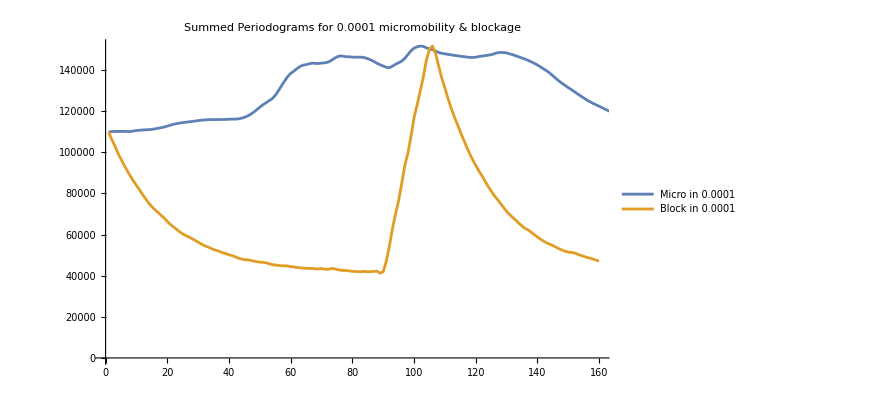

```mathematica
ListLinePlot[{sumPeriodograms5,sumPeriodograms4-114607},PlotRange->{{0,160},All},PlotStyle->{BlueGray},PlotLabel->"Summed Periodograms for 0.0001 micromobility & blockage",PlotLegends->Placed[{"Micro in 0.0001","Block in 0.0001"},{0.3,0.6}]]
```